```mathematica
ClearAll
Clear[β1,β2,δ1,γ1,p,ϵL,ϵLA,S,V,n,ϵa,r,α]
R=(((1-p)*β2)/γ1)*(1-ϵLA*(((1-ϵa)*r)/(α+(1-ϵa)*r))) + ((p*β1)/(γ1+δ1))*(1-ϵL*(((1-ϵa)*r)/(α+(1-ϵa)*r)))

A=D[R,β1]*(β1/R)
B=D[R,β2]*(β2/R)
Y=D[R,γ1]*(γ1/R)
G=D[R,δ1]*(δ1/R)
H=D[R,p]*(p/R)
J=D[R,ϵLA]*(ϵLA/R)
U=D[R,ϵL]*(ϵL/R)
S=D[R,ϵa]*(ϵa/R)
P=D[R,r]*(r/R)
M=D[R,α]*(α/R)
```

ClearAll

(p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1

(p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/((γ1+δ1) ((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))

((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/(γ1 ((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))

(γ1 (-(p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)^2-((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1^2))/((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1)

-(p β1 δ1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/((γ1+δ1)^2 ((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))

(p ((β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)-(β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))/((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1)

-((1-p) r β2 (1-ϵa) ϵLA)/(γ1 (α+r (1-ϵa)) ((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))

-(p r β1 (1-ϵa) ϵL)/((γ1+δ1) (α+r (1-ϵa)) ((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1))

(ϵa ((p β1 ((r ϵL)/(α+r (1-ϵa))-(r^2 (1-ϵa) ϵL)/(α+r (1-ϵa))^2))/(γ1+δ1)+((1-p) β2 ((r ϵLA)/(α+r (1-ϵa))-(r^2 (1-ϵa) ϵLA)/(α+r (1-ϵa))^2))/γ1))/((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1)

(r ((p β1 (-((1-ϵa) ϵL)/(α+r (1-ϵa))+(r (1-ϵa)^2 ϵL)/(α+r (1-ϵa))^2))/(γ1+δ1)+((1-p) β2 (-((1-ϵa) ϵLA)/(α+r (1-ϵa))+(r (1-ϵa)^2 ϵLA)/(α+r (1-ϵa))^2))/γ1))/((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1)

(α ((p r β1 (1-ϵa) ϵL)/((γ1+δ1) (α+r (1-ϵa))^2)+((1-p) r β2 (1-ϵa) ϵLA)/(γ1 (α+r (1-ϵa))^2)))/((p β1 (1-(r (1-ϵa) ϵL)/(α+r (1-ϵa))))/(γ1+δ1)+((1-p) β2 (1-(r (1-ϵa) ϵLA)/(α+r (1-ϵa))))/γ1)

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵL=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
A
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.299816

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
B
```

0.2

0.033

0.00018256

0.037

0.12

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

0.700184

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
Y
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

-0.998528

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
G
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

-0.00147204

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
H
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

0.204336

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
J
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

-1.54425

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
S=1
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
U
```

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

1

0.003545

0.00273

0.030421

0.913

-1.54598

0.2

0.033

0.00018256

0.037

0.12

0.913

0.75

1

1

0.003545

0.00273

0.030421

0.913

(0.00273 ((27.7631 (1-q) β4 ϵLB)/γ2+(27.7631 q β3 ϵLB)/(γ2+δ2)))/(((1-q) β4 (1-0.917381 ϵLB))/γ2+(q β3 (1-0.917381 ϵLB))/(γ2+δ2))

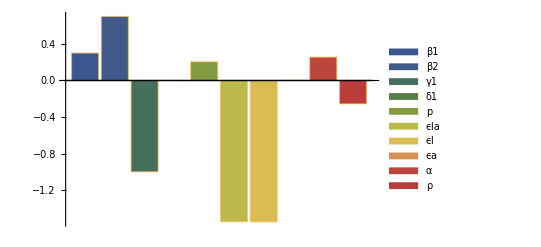

```mathematica
β1=0.2
β2=0.033
δ1=0.00018256
γ1=0.037
p=0.12
ϵl=0.913
ϵLA=0.75
V=1
n=1
ϵa=0.003545
α=0.00273
r=0.030421
ϵL=0.913
M















BarChart[{0.3,0.7001,-0.9979,-0.0020472,0.2043,-1.54425,-1.5459,0.0009083,0.2553,-0.2553},ChartLegends->{"β1","β2","γ1","δ1","p","ϵla","ϵl","ϵa","α","ρ"}, ChartStyle->"DarkRainbow"]
```